```mathematica
imageset1VoxelVol= (Quantity[141.70, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"];
imageset2VoxelVol= (Quantity[125.03, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"];
imageset3VoxelVol= (Quantity[151.82, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"];
```

```mathematica
orderFiles[dir_]:=Module[{filenames,order},
filenames=Import[dir];
order=Ordering@*Flatten@StringCases[filenames,x_~~y:DigitCharacter..~~".tif":> ToExpression@y];
filenames[[order]]
];
```

```mathematica
generateMesh[dir_String,voxelVol_]:=Module[{filenames,masks,im3d,morpComp,dim,dimtake,im3d2,mesh},
filenames=orderFiles[dir];
masks=Binarize@Import[dir<>#]&/@filenames;
im3d=Image3D@masks;
morpComp=MorphologicalComponents[im3d];
dim=First@ImageDimensions[im3d];
dimtake=MapAt[#-1&,
(MapAt[dim-#&,Reverse@Thread[Last@@ComponentMeasurements[morpComp,"BoundingBox"]],{2}]//Round)/. 0->1,{1,2}];
im3d2=Image3D[ImageTake[im3d,Sequence@@dimtake],BoxRatios->{1, 1, 1},ImageSize->Tiny];
Print[im3d2];
mesh=ImageMesh[im3d2,Method->"DualMarchingCubes",BoxRatios->{1, 1, 1},ImageSize->Tiny];
Print[{#,voxelVol*Abs@Volume[#]}&@mesh];
Print[{#,voxelVol*Abs[Volume[#]]}&@ImageMesh[GaussianFilter[im3d2,3],Method-> "DualMarchingCubes",BoxRatios->{1, 1, 1},ImageSize->Tiny]];
];
```

```mathematica
fitEllipsoid3D[image_Image3D]:=Block[{im,pixpos,meanpos,convexHull,mesh,points,minval,rules,ainv,centre,Σ,ellipsoidLJ,U,λ,U2},
im=image;
pixpos=PixelValuePositions[im,1];
meanpos=N@Mean[pixpos];
convexHull=ConvexHullMesh[#-meanpos&/@pixpos,BoxRatios->{1, 1, 1}];Print[mesh=DiscretizeRegion[convexHull,BoxRatios->{1, 1, 1},ImageSize->Tiny]];
points=MeshPrimitives[mesh,0]/.Point->Sequence;
 {minval,rules}=NMinimize[{-Log[Det[a]],{a(\[VectorGreaterEqual])_ 0, Table[Norm[a.xi+b]≤1, {xi,points}]}}, {a,b∈Vectors[3]}];
ainv=Inverse[a/.rules];
centre=-ainv.(b/.rules);
Σ=ainv.ainv;
ellipsoidLJ=Ellipsoid[centre,Σ];
Print@Graphics3D[{PointSize[0.01],Black,Point[points],Opacity[.2],Blue,ellipsoidLJ},
Axes->True,BoxRatios->{1,1,1},ImageSize->Medium];
{U,λ,U2}=SingularValueDecomposition[Σ];
{Sqrt@Diagonal[λ],Sqrt@Eigensystem[Σ][[1]]}
];
```

```mathematica
fitEllipsoid3DAlt[image_Image3D]:=Block[{im,pixpos,meanpos,convexHull,mesh,points,minval,rules,ainv,centre,Σ,ellipsoidLJ,U,λ,U2},
im=image;
pixpos=PixelValuePositions[MorphologicalPerimeter@im,1];
meanpos=N@Mean[pixpos];
points=#-meanpos&/@pixpos;
 {minval,rules}=NMinimize[{-Log[Det[a]],{a(\[VectorGreaterEqual])_ 0, Table[Norm[a.xi+b]≤1, {xi,points}]}}, {a,b∈Vectors[3]}];
ainv=Inverse[a/.rules];
centre=-ainv.(b/.rules);
Σ=ainv.ainv;
ellipsoidLJ=Ellipsoid[centre,Σ];
Print@Graphics3D[{PointSize[0.01],Black,Point[points],Opacity[.2],Blue,ellipsoidLJ},
Axes->True,BoxRatios->{1,1,1},ImageSize->Medium];
{U,λ,U2}=SingularValueDecomposition[Σ];
{Sqrt@Diagonal[λ],Sqrt@Eigensystem[Σ][[1]]}
];
```

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@3D cell shape classifier\\72 hrs\\";
```

## E-cadherin expressing cells

### cell-1

```mathematica
generateMesh[dir<>"image 1\\ecad\\cell-1\\",imageset1VoxelVol]
```

### cell-2

```mathematica
generateMesh[dir<>"\\image 2\\ecad\\cell-1\\",imageset2VoxelVol]
```

### cell-3

```mathematica
generateMesh[dir<>"\\image 2\\ecad\\cell-2\\",imageset2VoxelVol]
```

### cell-4

```mathematica
generateMesh[dir<>"\\image 3\\ecad\\cell-1\\",imageset3VoxelVol]
```

### cell-5

```mathematica
generateMesh[dir<>"\\image 3\\ecad\\cell-2\\",imageset3VoxelVol]
```

## E-cadherin-Brachyury cells

### cell-1

```mathematica
generateMesh[dir<>"\\image 1\\ecad-brach\\cell-1\\",imageset1VoxelVol]
```

### cell-2

```mathematica
generateMesh[dir<>"\\image 1\\ecad-brach\\cell-2\\",imageset1VoxelVol]
```

### cell-3

```mathematica
generateMesh[dir<>"\\image 1\\ecad-brach\\cell-3\\",imageset1VoxelVol]
```

### cell-4

```mathematica
generateMesh[dir<>"\\image 1\\ecad-brach\\cell-4\\",imageset1VoxelVol]
```

### cell-5

```mathematica
generateMesh[dir<>"\\image 1\\ecad-brach\\cell-5\\",imageset1VoxelVol]
```

### cell-6

```mathematica
generateMesh[dir<>"\\image 1\\ecad-brach\\cell-6\\",imageset1VoxelVol]
```

### cell-7

```mathematica
generateMesh[dir<>"\\image 1\\ecad-brach\\cell-7\\",imageset1VoxelVol]
```

## Brachyury expressing cells

### cell-1

```mathematica
generateMesh[dir<>"\\image 1\\brach\\cell-1\\",imageset1VoxelVol]
```

### cell-2

```mathematica
generateMesh[dir<>"\\image 3\\brach\\cell-1\\",imageset3VoxelVol]
```

### cell-3

```mathematica
generateMesh[dir<>"\\image 3\\brach\\cell-2\\",imageset3VoxelVol]
```

### cell-4

```mathematica
generateMesh[dir<>"\\image 3\\brach\\cell-3\\",imageset3VoxelVol]
```

## cluster analysis

```mathematica
EBImages={-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-};
ecadImages={-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-};
BrachImages={-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-};
```

## Minimal Ellipsoidal Fit (Conic Optimization)

```mathematica
SeedRandom[1];
n=3;
points=RandomPoint[Ball[],5000];
```

```mathematica
{minval,rules}=NMinimize[{-Log[Det[a]],{a(\[VectorGreaterEqual])_ 0, Table[Norm[a.xi+b]≤1, {xi,points}]}}, {a,b∈Vectors[n]}]
```

{-0.00235442,{a→{{0.999486,-0.000628021,-0.000618221},{-0.000628021,1.00056,0.000193685},{-0.000618221,0.000193685,1.00231}},b→{0.000643215,-0.000410424,0.0000827028}}}

```mathematica
ainv=Inverse[a/.rules];
centre=-ainv.(b/.rules);
Σ=ainv.ainv;
RegionMeasure[ellipsoidLJ=Ellipsoid[centre,Σ]]
```

4.17894

```mathematica
Graphics3D[{PointSize[0.01],Point[points],Opacity[.25],Green,ellipsoidLJ},BoxRatios->{1,1,1},ImageSize->Small]
```

-Graphics3D-

```mathematica
(*almost a minimal bounding sphere*)
```

```mathematica
{U,λ,U2}=SingularValueDecomposition[Σ];
{Sqrt@Diagonal[λ],Sqrt@*First@Eigensystem[Σ]}
```

{{1.00088,0.999259,0.997512},{1.00088,0.999259,0.997512}}

```mathematica
(*rotation matrix for aligning ellipsoid with x-axis *)
```

```mathematica
rot=Det[U]Transpose[U];
w=NullSpace[rot-IdentityMatrix[3]][[1]];
V=RotationMatrix[{{1,0,0},w}];
θ=-ArcTan@@(Transpose[V].rot.V)[[2,2;;3]];
Max[Abs[RotationMatrix[θ,w]-rot]]
```

2.22045×10^-16

```mathematica
Show[Graphics3D[{Opacity[0.5],Red,ellipsoidLJ,Blue,Rotate[#,θ,w,centre]&@ellipsoidLJ},Lighting->"Neutral"],Axes-> True,ImageSize->Small]
```

-Graphics3D-

## Fitting ellipsoids to cells

```mathematica
n=3;
```

```mathematica
im=ecadImages[[1]];
pixpos=PixelValuePositions[im,1];
meanpos=N@Mean[pixpos];
convexHull=ConvexHullMesh[#-meanpos&/@pixpos,BoxRatios->{1, 1, 1}];
mesh=DiscretizeRegion[convexHull,BoxRatios->{1, 1, 1},ImageSize->Tiny]
data=MeshPrimitives[mesh,0]/.Point->Sequence;
points=data;
 {minval,rules}=NMinimize[{-Log[Det[a]],{a(\[VectorGreaterEqual])_ 0, Table[Norm[a.xi+b]≤1, {xi,points}]}}, {a,b∈Vectors[n]}]
```

-Graphics3D-

{11.0103,{a→{{0.0112324,0.00105764,0.00229418},{0.00105764,0.011457,-0.00160078},{0.00229418,-0.00160078,0.130337}},b→{0.037816,-0.0448601,-0.0277083}}}

```mathematica
ainv=Inverse[a/.rules];
center=-ainv.(b/.rules);
Σ=ainv.ainv;
RegionMeasure[ellipsoidLJ=Ellipsoid[center,Σ]]
```

253402.

```mathematica
Graphics3D[{PointSize[0.01],Point[points],Opacity[.25],Green,ellipsoidLJ},Axes->True,BoxRatios->{1,1,1},ImageSize->Small]
```

-Graphics3D-

```mathematica
{U,λ,U2}=SingularValueDecomposition[Σ];
{Sqrt@Diagonal[λ],Sqrt@Eigensystem[Σ][[1]]}
```

{{97.8773,80.5979,7.6686},{97.8773,80.5979,7.6686}}

## Feature analysis

### Volumes

```mathematica
volumeEcad={Quantity[1321.05, ("Micrometers")^3],Quantity[1924.66, ("Micrometers")^3],Quantity[677.53, ("Micrometers")^3],Quantity[1213.72, ("Micrometers")^3],Quantity[1148.42, ("Micrometers")^3]};
volumeEB={Quantity[972.11, ("Micrometers")^3],Quantity[757.41, ("Micrometers")^3],Quantity[679.29, ("Micrometers")^3],Quantity[1104.55, ("Micrometers")^3],Quantity[934.12, ("Micrometers")^3],Quantity[1161.88, ("Micrometers")^3],Quantity[806.99, ("Micrometers")^3]};
volumeBrach={Quantity[386.39, ("Micrometers")^3],Quantity[337.83, ("Micrometers")^3],Quantity[321.31, ("Micrometers")^3],Quantity[487.65, ("Micrometers")^3]};
```

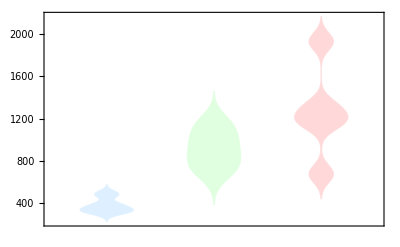

```mathematica
DistributionChart[{volumeBrach,volumeEB,volumeEcad},ChartStyle->{LightBlue,LightGreen,LightRed}]
```

```mathematica
Style[#2/#&@@Mean/@{volumeBrach,volumeEcad},Bold,LightPurple,40,FontFamily->"Arial Baltic"]
```

3.27966

```mathematica
Style[#2/#&@@Mean/@{volumeEB,volumeEcad},Bold,LightPurple,40,FontFamily->"Arial Baltic"]
```

1.37142

### Ellipsoids

```mathematica
ecadherinEllipsoidsR={
{97.8772539600239,80.59787415666926,7.668601461745319}*{141.70/1600,141.70/1600,1},
{224.00352926046963,212.0367706036181,8.29390476338982}*{125.03/1600,125.03/1600,1},
{172.68951929588525,143.56030473698863,5.161182557534426}*{125.03/1600,125.03/1600,1},
{93.42246303397758,90.36787452098542,6.960821673633064}*{151.82/1600,151.82/1600,1},
{122.64982910304444,112.81877536180713,6.180473356459843}*{151.82/1600,151.82/1600,1}
};
```

```mathematica
EBEllipsoidsR={
{204.96075838180317,117.9796050443396,6.7383599114673425}*{141.70/1600,141.70/1600,1},
{151.40811016649369,150.79858157082901,5.167403283295785}*{141.70/1600,141.70/1600,1},
{130.872938516569,107.55162654094948,5.215534828364961}*{141.70/1600,141.70/1600,1},
{149.22766269506036,135.05411486281054,6.787023267620833}*{141.70/1600,141.70/1600,1},
{243.5827651634381,179.1949440584098,5.122315071971005}*{141.70/1600,141.70/1600,1},
{197.87671617688113,146.3024455334606,5.14782018934413}*{141.70/1600,141.70/1600,1},
{317.2735222978239,285.7030290171748,4.05356591754579}*{141.70/1600,141.70/1600,1}
};
```

```mathematica
brachEllipsoidsR={
{145.0391022326775,126.69100704350369,4.6501744374491585}*{141.70/1600,141.70/1600,1},
{112.12368536189715,94.54080677530672,4.701291413492366}*{151.82/1600,151.82/1600,1},
{127.54063521063185,80.01538960713386,4.165267584347247}*{151.82/1600,151.82/1600,1},
{210.4967006458754,117.98574626749594,4.106391960438317}*{151.82/1600,151.82/1600,1}
};
```

### Clusterfy

```mathematica
dataToCluster=RandomSample[Thread[Transpose[{QuantityMagnitude@volumeBrach,brachEllipsoidsR}]-> "Brach"]~Join~Thread[Transpose[{QuantityMagnitude@volumeEcad,ecadherinEllipsoidsR}]->"Ecad"]~Join~Thread[Transpose[{QuantityMagnitude@volumeEB,EBEllipsoidsR}]-> "EB"]];
```

```mathematica
datafeatureplt=RandomSample@Cases[
dataToCluster,HoldPattern[x_->y:"Ecad"|"Brach"|"EB"]:>
Which[y=="Ecad", Style[Callout[x,y],Red],y=="Brach", Style[Callout[x,y],Blue],True,
Style[Callout[x,y],Green]]
];

FeatureSpacePlot[datafeatureplt,Method->"TSNE",
PlotStyle->Directive[Opacity[0.3],PointSize[0.04]],
ImageSize->Medium,Frame->True,AxesLabel->False]
```

-Graphics-

```mathematica
trainingdata=MapThread[<|"vol"-> #1,"ellipse"->#2|>->#3&,{QuantityMagnitude@Join[volumeBrach,volumeEcad,volumeEB],Join[brachEllipsoidsR,ecadherinEllipsoidsR,EBEllipsoidsR],
Join[ConstantArray["Brach",4],ConstantArray["Ecad",5],ConstantArray["EB",7]]}]/.PatternSequence[p:<|"vol"->677.53,"ellipse"->{13.494606623477832,11.218340563291054,5.161182557534426}|>->q:"Ecad"] :> p->"EB" ;
```

```mathematica
Clear[classifier];
```

```mathematica
classifier=Classify[trainingdata,Method->"NeuralNetwork",TargetDevice->"GPU",PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
And@@(SameQ@@@Thread[{classifier@Keys[trainingdata],Values@trainingdata}])
```

True

```mathematica
(*DumpSave["C:\\Users\\aliha\\Desktop\\analysis notebooks\\3D shape analysis\\classifier72.mx",classifier]*)
```

```mathematica
(*testingData is located in union classifier.nb*)
```

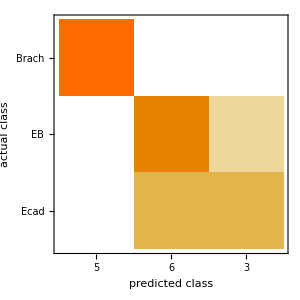

```mathematica
ClassifierMeasurements[classifier,testingData,"ConfusionMatrixPlot"]
```